# A Practitioner’s Guide to Best Practices in Data Visualization

## Jeffrey D. Camm, Michael J. Fry, Jeffrey Shaffer

## The Goal and Three General Principles:

First General Principle: design and layout matter 
Second General Principle: avoid clutter...the simpler the better
Third General Principle: use color purposely and effectively

## An Example: Barring Pie Charts

Find percentage of students declaring each of 12 categories of majors in college of business. 
Goal: Illustrate the part-to-whole relationship/percentage breakdown

Potential drawbacks:
-difficult to see legend and colors associated
-difficult to compare, because the view must move between legend and pie
-colors can be too similar
-3D does not facilitate understanding of data

Figure 1. This Three-Dimensional Pie Chart Shows the Percentage of Undergraduates by Major for a College of Business

Association ( <|…|> ) — an association between keys and values

<|…|>[key] — extract the value associated with any given key

```mathematica
PieChart3D[<|"Entrepreneurship"->26,"Operations management"-> 8,"Hospitality management" ->1,"Undesignated"->6,"Accounting"->19,"Real Estate" ->4,"Economics" ->2,"Informations Systems" ->4,"Finance"->17,"Business economics" ->1,"Industrial systems"->2,"Marketing" ->5,"Economics" -> 5|>, LabelingFunction-> "VerticalCallout",ChartLegends->{"Entrepreneurship","Operations management","Hospitality management","Undesignated","Accounting","Real Estate" ,"Economics","Informations Systems","Finance","Business economics","Industrial systems","Marketing","Economics"},PlotLabel->"Undergraduate majors" ]
```

-Graphics3D-

Figure 2. Compared to the Three-Dimensional Pie Chart in Figure 1, the Data-Ink Ratio in This Pie Chart Is Higher and the Chart Is Easier to Understand

```mathematica
PieChart[<|"Entrepreneurship"->26,"Operations management"-> 8,"Hospitality management" ->1,"Undesignated"->6,"Accounting"->19,"Real Estate" ->4,"Economics" ->2,"Informations Systems" ->4,"Finance"->17,"Business economics" ->1,"Industrial systems"->2,"Marketing" ->5,"Economics" -> 5|>, LabelingFunction-> "VerticalCallout",ChartLegends->{"Entrepreneurship","Operations management","Hospitality management","Undesignated","Accounting","Real Estate" ,"Economics","Informations Systems","Finance","Business economics","Industrial systems","Marketing","Economics"},PlotLabel->"Undergraduate majors" ]
```

-Graphics-

A vertical bar chart would be easier to visualize the differences.

Figure 3. In This Bar Chart, Different Colors Are No Longer Necessary to Distinguish Between Majors; Thus, We Can Eliminate the Legend

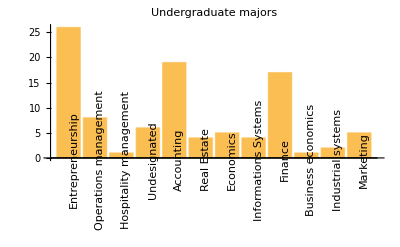

```mathematica
BarChart[<|"Entrepreneurship"->26,"Operations management"-> 8,"Hospitality management" ->1,"Undesignated"->6,"Accounting"->19,"Real Estate" ->4,"Economics" ->2,"Informations Systems" ->4,"Finance"->17,"Business economics" ->1,"Industrial systems"->2,"Marketing" ->5,"Economics" -> 5|>,PlotLabel->"Undergraduate majors" ,LabelingFunction-> "VerticalCallout",ChartLabels->Placed[{"Entrepreneurship","Operations management","Hospitality management","Undesignated","Accounting","Real Estate" ,"Economics","Informations Systems","Finance","Business economics","Industrial systems","Marketing","Economics"},Axis, Rotate[#,Pi/2]&] ]
```

How to improve figure 3: 
- sort the data from high to low

Figure 4. Sorting a Bar Chart Allows a Reader to Easily and Quickly Compare Differences Among Variables

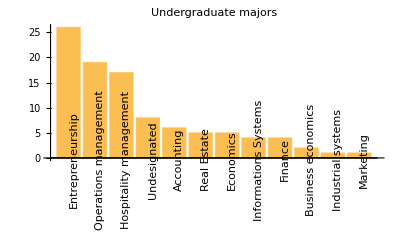

```mathematica
BarChart[Sort[<|"Entrepreneurship"->26,"Operations management"-> 8,"Hospitality management" ->1,"Undesignated"->6,"Accounting"->19,"Real Estate" ->4,"Economics" ->2,"Informations Systems" ->4,"Finance"->17,"Business economics" ->1,"Industrial systems"->2,"Marketing" ->5,"Economics" -> 5|>, Greater],PlotLabel->"Undergraduate majors" ,LabelingFunction-> "VerticalCallout",ChartLabels->Placed[{"Entrepreneurship","Operations management","Hospitality management","Undesignated","Accounting","Real Estate" ,"Economics","Informations Systems","Finance","Business economics","Industrial systems","Marketing","Economics"},Axis, Rotate[#,Pi/2]&] ]
```

Display horizontally in order to read the categorical text labels. Make it as simple as possible. 
We also remove the axis, because it is not necessary to find the three largest majors.

Figure 5. The Categorical Text Labels Are Horizontal; Thus, the Chart Is Easier to Read Than the Vertical Bar Chart in Figure 4

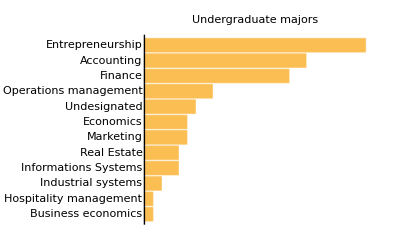

```mathematica
BarChart[Sort[<|"Entrepreneurship"->26,"Operations management"-> 8,"Hospitality management" ->1,"Undesignated"->6,"Accounting"->19,"Real Estate" ->4,"Economics" ->2,"Informations Systems" ->4,"Finance"->17,"Business economics" ->1,"Industrial systems"->2,"Marketing" ->5,"Economics" -> 5|>, Less],PlotLabel->"Undergraduate majors" ,BarOrigin->Left, ChartLabels->Automatic,Axes->{True,False}]
```

Three general principles illustrated by figure 1-5

1. Design and layout matter. Use them effectively
2. Avoid clutter, too many labels, values, lines and dimensions create noise
3 Use color effectively
4. Avoid using a pie chart
5. Sort the data. It facilitates comparison
6. Avoid rotated text

## Design and Layout matter: Types of Comparisons and Chart Types

Categorical comparison: 

Figure 6. (Color online) Bar Charts for Categorical Comparisons Can Be Augmented with a Target Line

```mathematica
Table[BarChart[Sort[<|"Bananas" -> 23, "Apples" -> 17, "Grapes" -> 14, "Oranges"-> 12|>],LabelingFunction->o,ChartLabels->Automatic,BarOrigin ->o,PlotLabel->"Bar chart for categorical comparisons",Axes->{True,False}],{o,{Left,Bottom}}]
```

Make it easy to for the eye to follow. As pictured above:
- if the data labels provide the actual labels, don't use axis labels
- avoid rotated text, rotate the chart instead
- mute or remove gridlines and chart boarders
- use a light font color on dark colored bars

To format a part-to-whole comparison: instead of using a pie chart, use a stacked bar chart.

Figure 7. (Color online) A Stacked Bar Chart Can Enhance a Bar Chart and Is Generally Preferable to a Pie Chart for Making
Part-to-Whole Comparisons

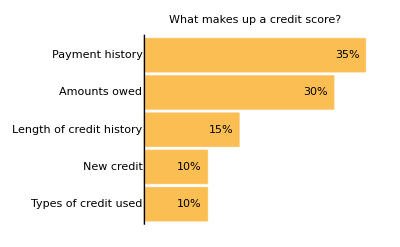

```mathematica
BarChart[Sort[<|"Payment history"->35,"Amounts owed"->30,"Length of credit history"->15,"Types of credit used"->10,"New credit"->10|>],ChartLabels->Automatic,LabelingFunction->(Placed[Row[{#,"%"}],Right]&),PlotLabel->"What makes up a credit score?",BarOrigin->Left,Axes->{True,False}]
```

HAD TROUBLE FIGURING OUT HOW TO PLOT percentages above the bar chart...while also keeping it to the right

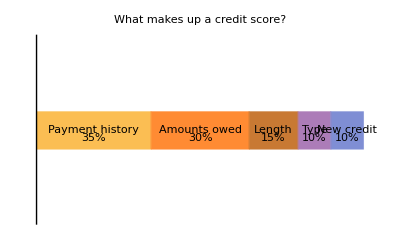

```mathematica
BarChart[Sort[<|"Payment history"->35,"Amounts owed"->30,"Length of credit history"->15,"Types of credit used"->10,"New credit"->10|>, Greater],ChartLabels ->Callout[{"Payment history","Amounts owed","Length","Type","New credit"},Center],LabelingFunction->(Placed[Row[{#,"%"}],Bottom]&),PlotLabel->"What makes up a credit score?",BarOrigin->Left, Axes->{True,False},BarSpacing ->Small,ChartLayout->"Stacked"]
```

```mathematica
Show[%14,ImageSize->Full]
```

-Graphics-

To show a trend over time: 
-plot time on the horizontal axis
-line chart or a bar chart
-downside to line chart is that it does not show all data values...the chart would appear too cluttered

Figure 8. Both Line Charts and Bar Charts Can Be Used Effectively for Time-Series Data

```mathematica
Halloween = Import["/Users/SarahJune/Documents/2018-2019/Coding Stuff/STATS II/Data Visualization/Halloween.csv"]
```

{{Year,Number of trick-or-treaters},{2017,776},{2016,822},{2015,747},{2014,454},{2013,391},{2012,673},{2011,869},{2010,726},{2009,542},{2008,492}}

```mathematica
TableForm[Halloween]
```

Year | Number of trick-or-treaters
2017 | 776
2016 | 822
2015 | 747
2014 | 454
2013 | 391
2012 | 673
2011 | 869
2010 | 726
2009 | 542
2008 | 492

```mathematica
Dimensions[{{"Year","Number of trick-or-treaters"},{2017,776},{2016,822},{2015,747},{2014,454},{2013,391},{2012,673},{2011,869},{2010,726},{2009,542},{2008,492}}]
```

```mathematica
{11,2}
Halloween["Year","Number of trick-or-treaters"]
```

{11,2}

{{Year,Number of trick-or-treaters},{2017,776},{2016,822},{2015,747},{2014,454},{2013,391},{2012,673},{2011,869},{2010,726},{2009,542},{2008,492}}[Year,Number of trick-or-treaters]

```mathematica
ListLinePlot[Halloween, PlotLabel->"Number of trick-or-treaters by year",PlotLabel->{Callout["869",{Scaled[2011],Above}],Callout["391",{Scaled[2013],Below}]}]
```

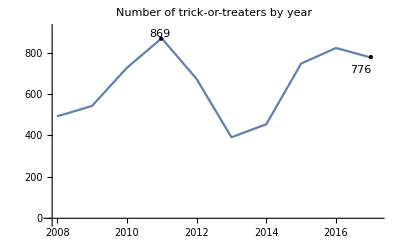

```mathematica
BarChart[Halloween,PlotLabel->"Number of trick-or-treaters by year"]
```

BarChart::ldata: {{Year,Number of trick-or-treaters},{2017,776},{2016,822},{2015,747},{2014,454},{2013,391},{2012,673},{2011,869},{2010,726},{2009,542},{2008,492}}[All,Year] is not a valid dataset or list of datasets.

BarChart[{{Year,Number of trick-or-treaters},{2017,776},{2016,822},{2015,747},{2014,454},{2013,391},{2012,673},{2011,869},{2010,726},{2009,542},{2008,492}}[All,Year],PlotLabel→Number of trick-or-treaters by year]

```mathematica
Halloween[All,"Year"]
```

{{Year,Number of trick-or-treaters},{2017,776},{2016,822},{2015,747},{2014,454},{2013,391},{2012,673},{2011,869},{2010,726},{2009,542},{2008,492}}[All,Year]

Use of dots:
-comparisons
-time-series data when interval is missing
-plotting a distribution
-showing a correlation between variables

If possible, avoid using shapes other than dots or circles...it is difficult to identify the center of triangles, squares, stars, etc. 

Figure 9.

```mathematica
exams =
Import["/Users/SarahJune/Documents/2018-2019/Coding Stuff/STATS II/Data Visualization/exams.csv"]
```

{{74},{82},{64},{63},{64},{59},{47},{75},{74},{71},{61},{71},{86},{69},{33},{77},{87},{82},{74},{42},{64},{35},{61},{70},{82},{69},{34},{52},{77},{50},{69},{58},{41},{82},{97},{75},{89},{62},{59},{71},{65},{77},{74},{61},{83},{53},{48},{81},{48},{61},{76},{47},{42},{63},{57},{31},{66},{70},{88},{53},{86},{72},{62},{47},{38},{58},{85},{53},{72},{81},{97},{47},{69},{84},{71},{81},{76},{50},{69},{78},{98},{85},{73},{78},{29},{55},{50},{84},{75},{71},{63},{84},{69},{65},{56},{84},{75},{62},{72},{80}}

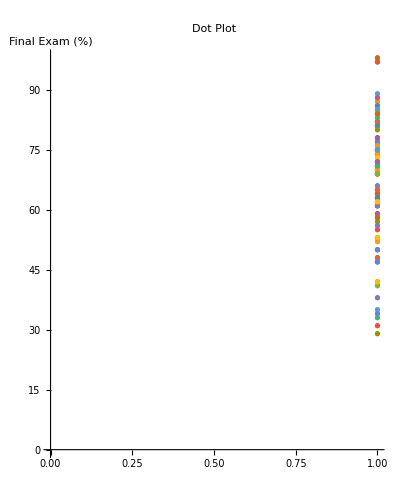

```mathematica
ListPlot[exams,AspectRatio -> 10/8,Axes->{False,True},PlotLabel->"Dot Plot",AxesLabel->"Final Exam (%)"]
```

**Make a jitter plot

Figure 10. A Scatter Diagram and Box Plots Can Display the Relationship Between Two Variables and Are
Useful for Displaying the Distributions of Correlated Variables

```mathematica
MLB = 
Import["/Users/SarahJune/Documents/2018-2019/Coding Stuff/STATS II/Data Visualization/MLB.csv"]
```

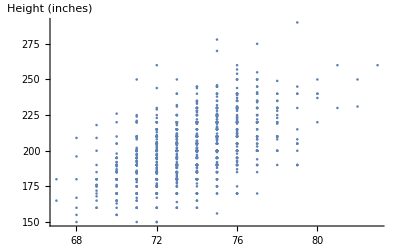

```mathematica
ListPlot[MLB,AxesLabel->"Height (inches)"]
```

```mathematica
ListPlot[Entity["Country","UnitedStates"]"Population Density"]
```

ListPlot::lpn: Population Density United States is not a list of numbers or pairs of numbers.

ListPlot[Population Density United States]